## Problem 1

```mathematica
a=1;
b=2;
```

```mathematica
Integrate[(r-a)/r^2,{r,a,r}]
```

ConditionalExpression[-1+1/r+Log[r], Re[r]>0||r∉ℝ]

```mathematica
Vb=Log[b/a]+a/b-1
```

-1/2+Log[2]

```mathematica
Integrate[(b-a)/r^2,{r,b,r}]
```

ConditionalExpression[1/2-1/r, Re[r]>0||r∉ℝ]

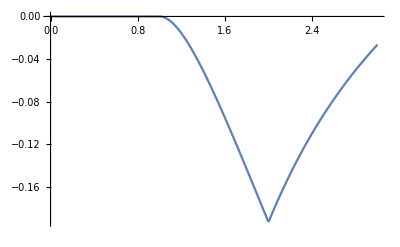

```mathematica
Plot[Piecewise[{{0,r<a},{-(Log[r/a]+a/r-a),a≤r≤b},{-(Vb-(-1/r+1/2)),b<r}}],{r,0,3}]
```

## Problem 2

```mathematica
Integrate[1/(2*Sqrt[u]),u]
```

√u

```mathematica
D[Sqrt[R^2+z^2]-z,z]
```

-1+z/(√(R^2+z^2))

## Problem 3

```mathematica
x=0.1;
y=0.2;
z=-0.1;
rho=2*10^-9;
```

```mathematica
1/(4*Pi*8.85*10^-12)*NIntegrate[rho/Sqrt[(x-xprime)^2+(y-yprime)^2+(z-zprime)^2],{xprime,-.2,.2},{yprime,-.3,.3},{zprime,0,.4},Exclusions->{{x,y,z}}]+1/(4*Pi*8.85*10^-12)*NIntegrate[-rho/Sqrt[(x-xprime)^2+(y-yprime)^2+(z-zprime)^2],{xprime,-.2,.2},{yprime,-.3,.3},{zprime,-.4,0},Exclusions->{{x,y,z}}]
```

-2.53241